```mathematica
SetDirectory[NotebookDirectory[]];
```

## Uloha 1

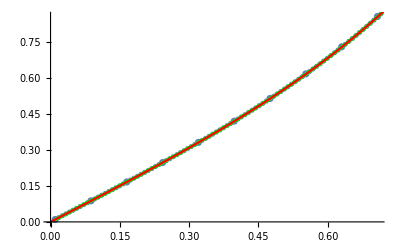

```mathematica
n10 = Import["./outputs/uloha1_10n.csv","CSV"];
n100 = Import["./outputs/uloha1_100n.csv","CSV"];
n1000 = Import["./outputs/uloha1_1000n.csv","CSV"];
DSolve[{x'[t]==x[t]*x[t]+1, x[0]==0},x,t];
Show[
ListPlot[n10],
ListLinePlot[n10],
ListPlot[n100],
ListLinePlot[n100],
ListPlot[n1000, PlotStyle->Green],
ListLinePlot[n1000, PlotStyle->Green],
Plot[Evaluate[x[t]/.%],{t,0,π/4}, PlotStyle->Red]
]
```

Riešenie z minulej hodiny :

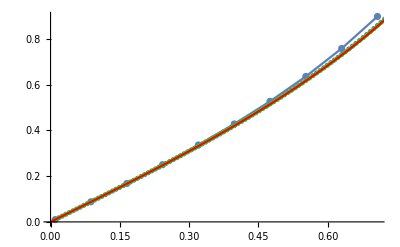

## Uloha 2

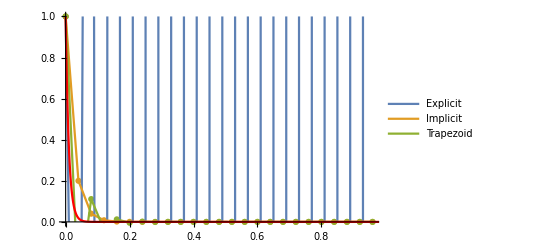

```mathematica
exp= Import["./outputs/uloha2_exp_25n.csv","CSV"];
imp= Import["./outputs/uloha2_imp_25n.csv","CSV"];
tra= Import["./outputs/uloha2_tra_25n.csv","CSV"];
Show[
ListPlot[{exp, imp, tra}, PlotRange->{0,1}],
ListLinePlot[{exp, imp, tra}, PlotLegends->{"Explicit", "Implicit", "Trapezoid"}, PlotRange->{0,1}],
Plot[Exp[-100 t],{t,0,1}, PlotStyle->Red, PlotRange->{0,1}]
]
```

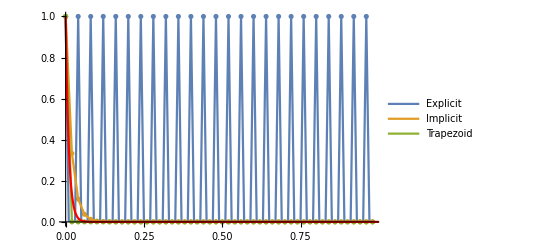

```mathematica
exp= Import["./outputs/uloha2_exp_50n.csv","CSV"];
imp= Import["./outputs/uloha2_imp_50n.csv","CSV"];
tra= Import["./outputs/uloha2_tra_50n.csv","CSV"];
Show[
ListPlot[{exp, imp, tra}, PlotRange->{0,1}],
ListLinePlot[{exp, imp, tra}, PlotLegends->{"Explicit", "Implicit", "Trapezoid"}, PlotRange->{0,1}],
Plot[Exp[-100 t],{t,0,1}, PlotStyle->Red, PlotRange->{0,1}]
]
```

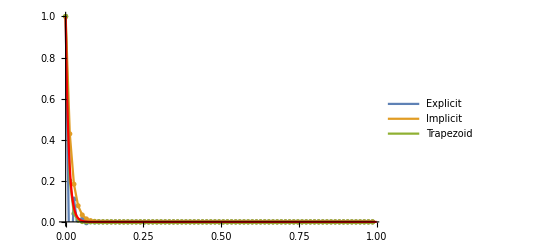

```mathematica
exp= Import["./outputs/uloha2_exp_75n.csv","CSV"];
imp= Import["./outputs/uloha2_imp_75n.csv","CSV"];
tra= Import["./outputs/uloha2_tra_75n.csv","CSV"];
Show[
ListPlot[{exp, imp, tra}, PlotRange->{0,1}],
ListLinePlot[{exp, imp, tra}, PlotLegends->{"Explicit", "Implicit", "Trapezoid"}, PlotRange->{0,1}],
Plot[Exp[-100 t],{t,0,1}, PlotStyle->Red, PlotRange->{0,1}]
]
```

{{x→Function[{t},ⅇ^(-100 t)]}}

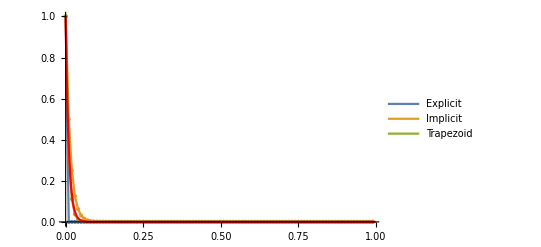

```mathematica
exp= Import["./outputs/uloha2_exp_100n.csv","CSV"];
imp= Import["./outputs/uloha2_imp_100n.csv","CSV"];
tra= Import["./outputs/uloha2_tra_100n.csv","CSV"];
DSolve[{x'[t]==-100 x[t], x[0]==1},x,t]
Show[
ListPlot[{exp, imp, tra}, PlotRange->{0,1}],
ListLinePlot[{exp, imp, tra}, PlotLegends->{"Explicit", "Implicit", "Trapezoid"}, PlotRange->{0,1}],
Plot[Exp[-100 t],{t,0,1}, PlotStyle->Red, PlotRange->{0,1}]
]
```